# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Quantum channel/QMB_offline copy.wl"];
Get["/Users/pcs/Desktop/Quantum channel/Chaometer.wl"];
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);

Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Chop[Total[Map[VNentropy,Chop[Eigenvalues[rho]]]]]
];
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
(*Define subsystem dimensions*)
(*Compute the Page value using the digamma function*)
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

# XXZ Regular

```mathematica
L=12;
h1=h2=1;
Δ=1.0;
H=OpenXXZHamiltonian[L,Δ,h1,h2];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
La=6;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,eigenvec},DistributedContexts->Full];
```

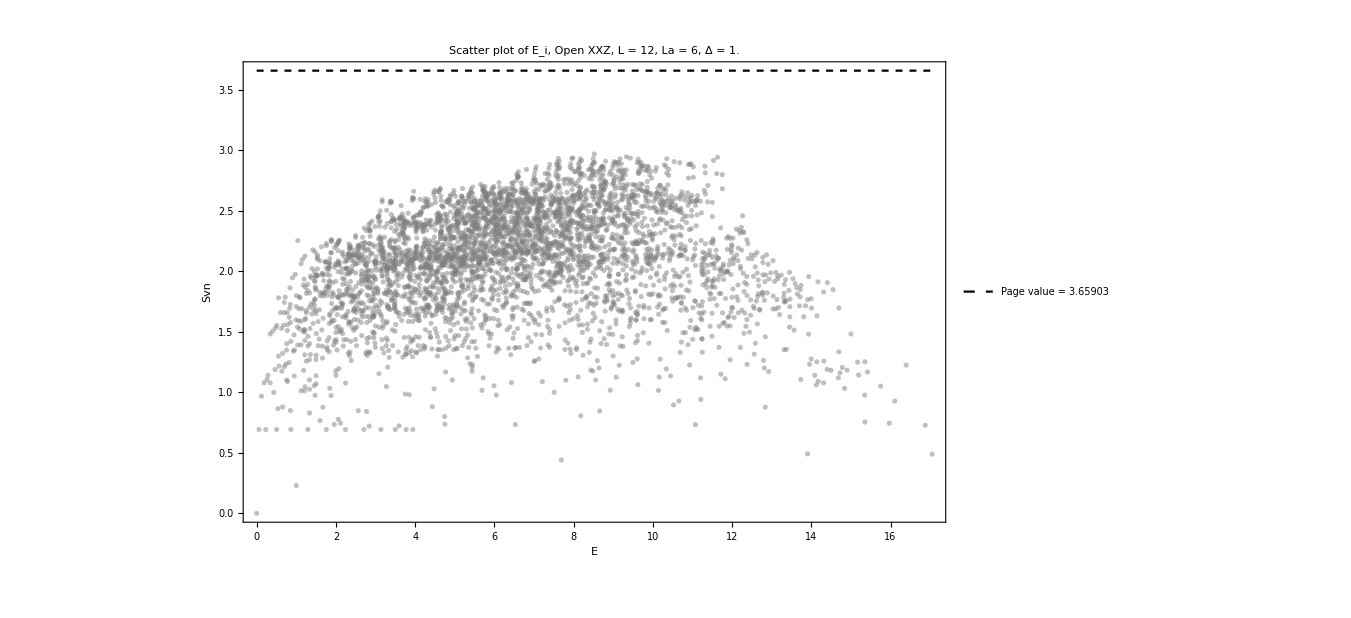

```mathematica
eigenvecentropy =Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open XXZ, L = "<>ToString[L]<>", La = "<>ToString[La]<>", Δ = "<>ToString[Δ]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

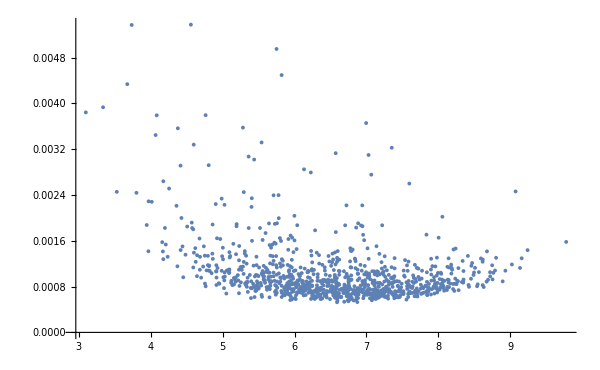

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
ListPlot[Transpose[{energies,iprs}],PlotRange->All,ImageSize->600]
```

```mathematica
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
productstate=data[[1;;10]][[All,3]];
(*tlist=Table[10^i,{i,-1,3,0.0008}];
tlist//Length*)
ti=0;
tf=1000;
Δt=0.5;
tlist=Table[i,{i,ti,tf,Δt}];
tlist//Length
```

2001

```mathematica
fakesvn=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

```mathematica
longmean=Table[Mean[fakesvn[[i]][[All,2]][[-500;;-1]]],{i,Length[productstate]}];
newenergies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate}];
```

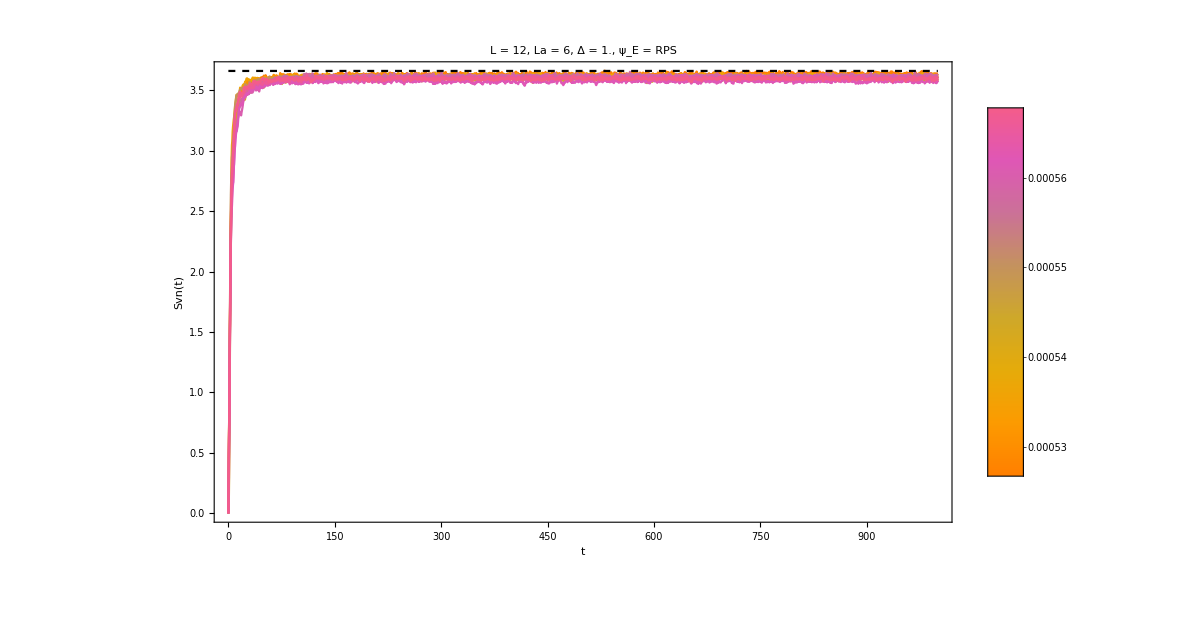

```mathematica
(*Step 1:Determine the overall energy range*)
sorted=data[[1;;10]][[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
(*Step 2:Define a function to map an energy value to a temperature-like color*)
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", Δ = "<>ToString[Δ]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots,Plot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Black,Dashed]}]}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
```

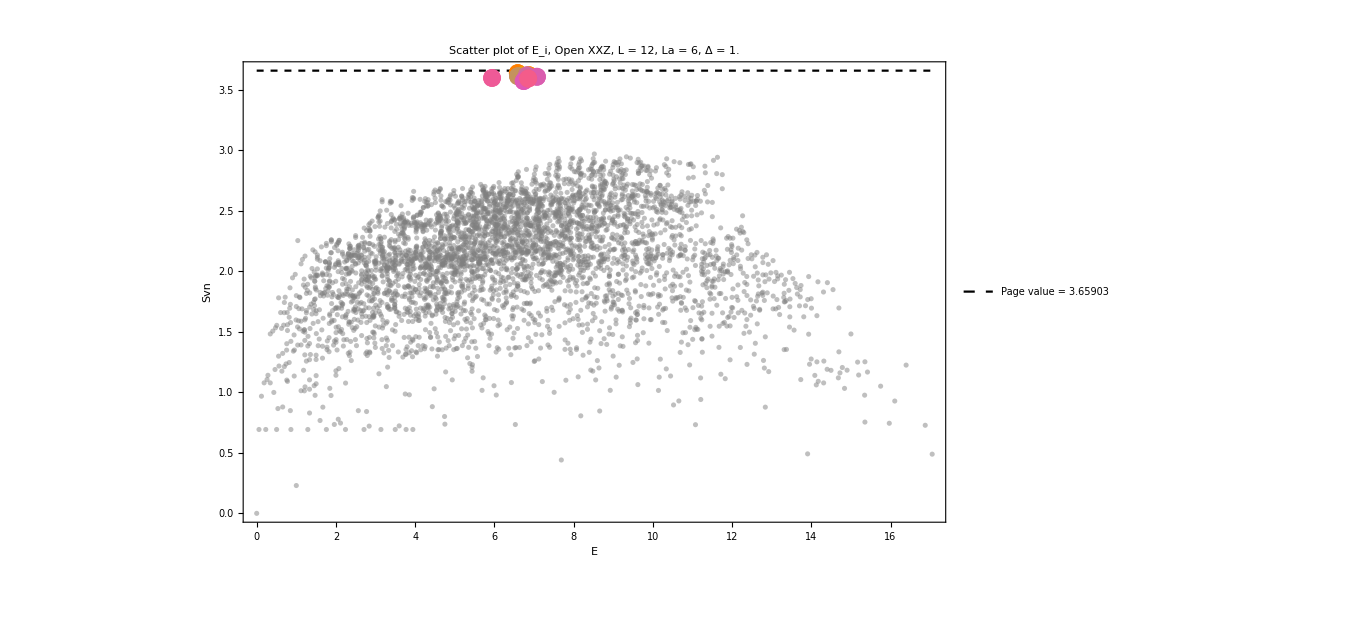

```mathematica
Show[{eigenvecentropy,Table[ListPlot[{{newenergies[[i]],longmean[[i]]}},PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}]}]
```

## Antiflatness

```mathematica
Clear[rhoa];
rhoa[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
MatrixPartialTrace[Dyad[state],2,{dima,dimb}]
];
Clear[antif];
antif[rho_]:=Tr[MatrixPower[rho,3]]-Tr[MatrixPower[rho,2]];
```

```mathematica
rhos=Table[ParallelTable[Chop[rhoa[L,La,Lb,i,eigenval,eigenvec,t]],{t,tlist},DistributedContexts->Full],{i,productstate}];
purity=Table[ParallelTable[{tlist[[i]],Tr[j[[i]].j[[i]]]},{i,Length[tlist]}],{j,rhos}];
flatness=Table[ParallelTable[{tlist[[i]],Chop[antif[j[[i]]]]},{i,Length[tlist]}],{j,rhos}];
```

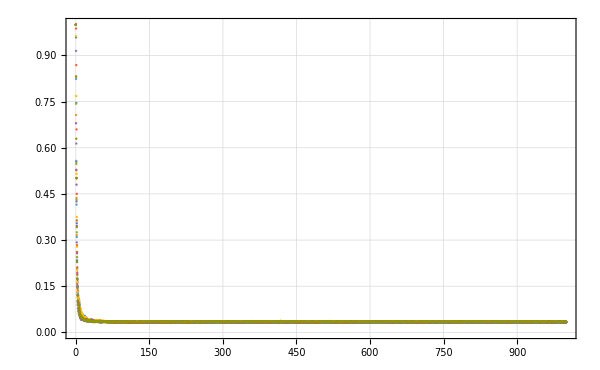

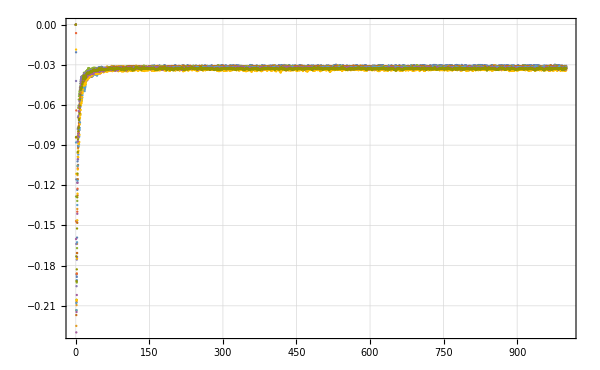

```mathematica
ListPlot[purity,PlotRange->All,PlotTheme->"Detailed",ImageSize->600]
ListPlot[flatness,PlotRange->All,PlotTheme->"Detailed",ImageSize->600]
```

```mathematica
list=purity[[1]];
interpregular=Table[Interpolation[i],{i,purity}];
meanpurityregular=Table[Quiet[NIntegrate[i[t]/(list[[-1,1]]-list[[1,1]]),{t,list[[1,1]],list[[-1,1]]}]],{i,interpregular}];
variancepurityregular=Table[Quiet[NIntegrate[(interpregular[[i]][t]-meanpurityregular[[i]])^2/(list[[-1,1]]-list[[1,1]]),{t,list[[1,1]],list[[-1,1]]}]],{i,Length[interpregular]}];
```

```mathematica
meanpurityregular
variancepurityregular
```

{0.0346526,0.034936,0.0347157,0.0370615,0.0353205,0.0354132,0.0360357,0.0377992,0.0360255,0.0364763}

{0.00113794,0.000733605,0.000758425,0.00138842,0.00094367,0.000928779,0.000855534,0.00118943,0.000733572,0.00092279}

```mathematica
list=flatness[[1]];
interpregular=Table[Interpolation[i],{i,flatness}];
meanflatnessregular=Table[Quiet[NIntegrate[i[t]/(list[[-1,1]]-list[[1,1]]),{t,list[[1,1]],list[[-1,1]]}]],{i,interpregular}];
varianceflatnessregular=Table[Quiet[NIntegrate[(interpregular[[i]][t]-meanflatnessregular[[i]])^2/(list[[-1,1]]-list[[1,1]]),{t,list[[1,1]],list[[-1,1]]}]],{i,Length[interpregular]}];
```

```mathematica
meanflatnessregular
varianceflatnessregular
```

{-0.0318868,-0.0325441,-0.0323396,-0.0338022,-0.0326816,-0.0327709,-0.0334234,-0.0346577,-0.0335365,-0.0336924}

{0.0000575509,0.0000830886,0.0000703125,0.0000523788,0.0000500694,0.0000840885,0.0000838125,0.0000734484,0.0000878397,0.0000596659}

# XXZ chaotic

```mathematica
L=12;
noise=Table[1*RandomReal[{-1,1}],{i,L}];
H=HeisenbergXXXwNoise[noise,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
La=6;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,eigenvec},DistributedContexts->Full];
```

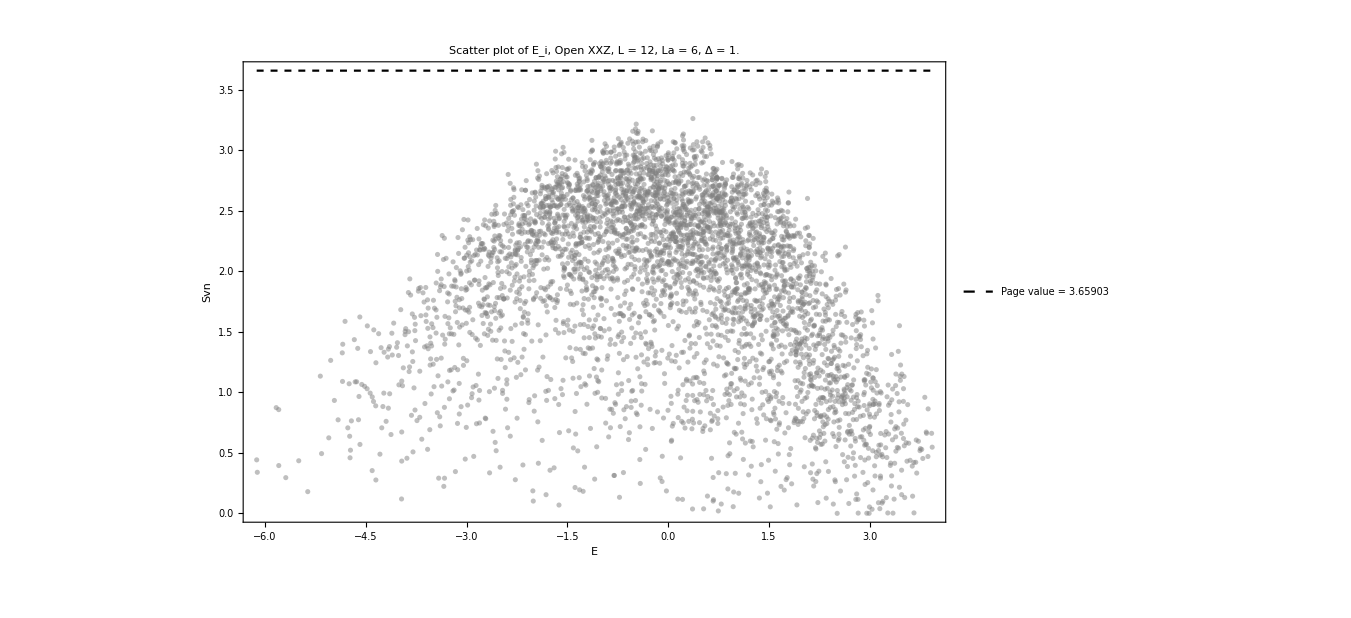

```mathematica
eigenvecentropy =Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open XXZ, L = "<>ToString[L]<>", La = "<>ToString[La]<>", Δ = "<>ToString[Δ]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

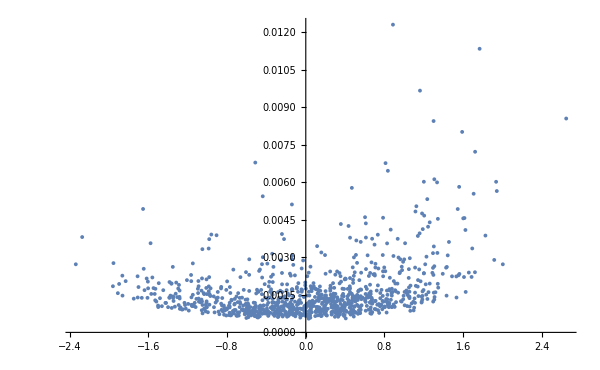

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
ListPlot[Transpose[{energies,iprs}],PlotRange->All,ImageSize->600]
```

```mathematica
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
productstate=data[[1;;10]][[All,3]];
(*tlist=Table[10^i,{i,-1,3,0.0008}];
tlist//Length*)
ti=0;
tf=1000;
Δt=0.5;
tlist=Table[i,{i,ti,tf,Δt}];
tlist//Length
```

2001

```mathematica
fakesvn=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

```mathematica
longmean=Table[Mean[fakesvn[[i]][[All,2]][[-500;;-1]]],{i,Length[productstate]}];
newenergies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate}];
```

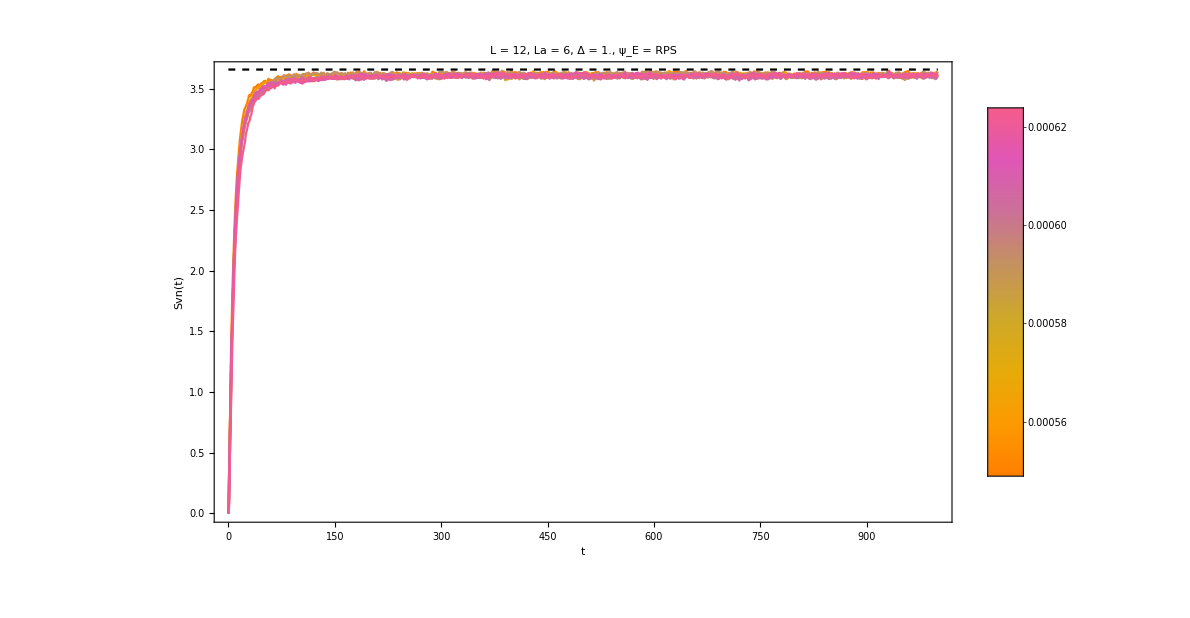

```mathematica
(*Step 1:Determine the overall energy range*)
sorted=data[[1;;10]][[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
(*Step 2:Define a function to map an energy value to a temperature-like color*)
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", Δ = "<>ToString[Δ]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots,Plot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Black,Dashed]}]}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
```

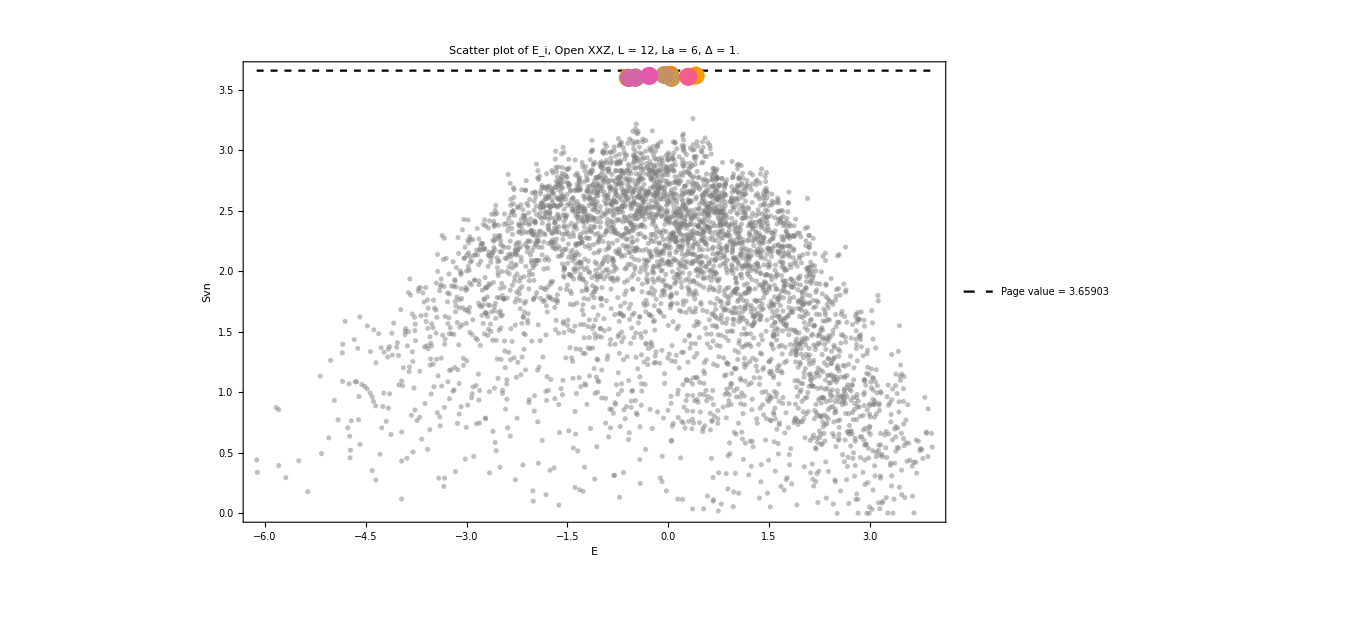

```mathematica
Show[{eigenvecentropy,Table[ListPlot[{{newenergies[[i]],longmean[[i]]}},PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}]}]
```

## Antiflatness

```mathematica
Clear[rhoa];
rhoa[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
MatrixPartialTrace[Dyad[state],2,{dima,dimb}]
];
Clear[antif];
antif[rho_]:=Tr[MatrixPower[rho,3]]-Tr[MatrixPower[rho,2]];
```

```mathematica
rhos=Table[ParallelTable[Chop[rhoa[L,La,Lb,i,eigenval,eigenvec,t]],{t,tlist},DistributedContexts->Full],{i,productstate}];
purity=Table[ParallelTable[{tlist[[i]],Tr[j[[i]].j[[i]]]},{i,Length[tlist]}],{j,rhos}];
flatness=Table[ParallelTable[{tlist[[i]],Chop[antif[j[[i]]]]},{i,Length[tlist]}],{j,rhos}];
```

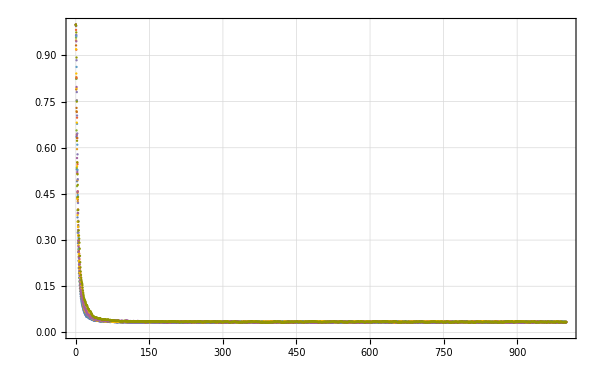

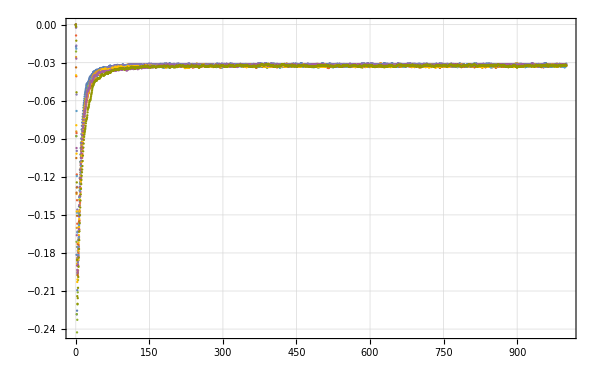

```mathematica
ListPlot[purity,PlotRange->All,PlotTheme->"Detailed",ImageSize->600]
ListPlot[flatness,PlotRange->All,PlotTheme->"Detailed",ImageSize->600]
```

```mathematica
list=purity[[1]];
interpcaos=Table[Interpolation[i],{i,purity}];
meanpuritycaos=Table[Quiet[NIntegrate[i[t]/(list[[-1,1]]-list[[1,1]]),{t,list[[1,1]],list[[-1,1]]}]],{i,interpcaos}];
variancepuritycaos=Table[Quiet[NIntegrate[(interpcaos[[i]][t]-meanpuritycaos[[i]])^2/(list[[-1,1]]-list[[1,1]]),{t,list[[1,1]],list[[-1,1]]}]],{i,Length[interpcaos]}];
```

```mathematica
meanpuritycaos
variancepuritycaos
```

{0.036975,0.0382446,0.038601,0.039901,0.0385998,0.0393429,0.0394693,0.0391343,0.0388798,0.0406658}

{0.0017403,0.00214977,0.00181527,0.00264885,0.00280092,0.00216291,0.00260253,0.00205014,0.00225582,0.0028307}

```mathematica
list=flatness[[1]];
interpcaos=Table[Interpolation[i],{i,flatness}];
meanflatnesscaos=Table[Quiet[NIntegrate[i[t]/(list[[-1,1]]-list[[1,1]]),{t,list[[1,1]],list[[-1,1]]}]],{i,interpcaos}];
varianceflatnesscaos=Table[Quiet[NIntegrate[(interpcaos[[i]][t]-meanflatnesscaos[[i]])^2/(list[[-1,1]]-list[[1,1]]),{t,list[[1,1]],list[[-1,1]]}]],{i,Length[interpcaos]}];
```

```mathematica
meanpuritycaos
variancepuritycaos
-meanflatnesscaos
varianceflatnesscaos
```

{0.036975,0.0382446,0.038601,0.039901,0.0385998,0.0393429,0.0394693,0.0391343,0.0388798,0.0406658}

{0.0017403,0.00214977,0.00181527,0.00264885,0.00280092,0.00216291,0.00260253,0.00205014,0.00225582,0.0028307}

{0.0333174,0.0338806,0.0347108,0.0347765,0.033497,0.0347907,0.0345354,0.0347927,0.0343681,0.0352427}

{0.000175156,0.000179257,0.00021422,0.000177136,0.000155593,0.000167092,0.000153,0.000183108,0.000176209,0.000240582}

```mathematica
meanpurityregular
variancepurityregular
-meanflatnessregular
varianceflatnessregular
```

{0.129195,0.128673,0.129819,0.132005,0.136908,0.131259,0.132217,0.130344,0.13862,0.12751}

{0.000706403,0.000970091,0.000669915,0.000939221,0.00122383,0.000942793,0.000750603,0.000634062,0.00101574,0.000823689}

{0.107458,0.106916,0.107956,0.109111,0.111799,0.108541,0.109315,0.108369,0.113089,0.106324}

{0.0000334373,0.0000319026,0.0000350445,0.0000364016,0.0000342013,0.0000440072,0.0000329611,0.0000409069,0.0000372703,0.0000348734}

{0.0672931,0.067535,0.0668459,0.0671185,0.0693197,0.0687369,0.0683984,0.0694096,0.0669617,0.0703983}

{0.000761048,0.000908989,0.000825576,0.000990677,0.000838959,0.000855667,0.000708592,0.00077068,0.00103736,0.000567978}

{0.0606539,0.0607443,0.0602847,0.0603117,0.0622429,0.061748,0.0616245,0.0623321,0.0601516,0.0634063}

{0.0000719524,0.0000464023,0.0000435105,0.0000529906,0.0000419291,0.0000549004,0.0000726261,0.000043223,0.0000392855,0.000046549}

{0.0346526,0.034936,0.0347157,0.0370615,0.0353205,0.0354132,0.0360357,0.0377992,0.0360255,0.0364763}

{0.00113794,0.000733605,0.000758425,0.00138842,0.00094367,0.000928779,0.000855534,0.00118943,0.000733572,0.00092279}

{0.0318868,0.0325441,0.0323396,0.0338022,0.0326816,0.0327709,0.0334234,0.0346577,0.0335365,0.0336924}

{0.0000575509,0.0000830886,0.0000703125,0.0000523788,0.0000500694,0.0000840885,0.0000838125,0.0000734484,0.0000878397,0.0000596659}

# Datos

## L = 8, La = 4

```mathematica
meanpuritycaos
variancepuritycaos
```

{0.133546,0.132113,0.136517,0.144075,0.139639,0.134033,0.133171,0.136108,0.137455,0.144501}

{0.00160625,0.00127644,0.00208019,0.00203863,0.00203858,0.00180378,0.00143949,0.0011095,0.00197461,0.00139853}

```mathematica
meanpurityregular
variancepurityregular
```

{0.129195,0.128673,0.129819,0.132005,0.136908,0.131259,0.132217,0.130344,0.13862,0.12751}

{0.000706403,0.000970091,0.000669915,0.000939221,0.00122383,0.000942793,0.000750603,0.000634062,0.00101574,0.000823689}

## L = 10, La = 5

```mathematica
meanpurityregular
variancepurityregular
-meanflatnessregular
varianceflatnessregular
```

{0.0672931,0.067535,0.0668459,0.0671185,0.0693197,0.0687369,0.0683984,0.0694096,0.0669617,0.0703983}

{0.000761048,0.000908989,0.000825576,0.000990677,0.000838959,0.000855667,0.000708592,0.00077068,0.00103736,0.000567978}

{0.0606539,0.0607443,0.0602847,0.0603117,0.0622429,0.061748,0.0616245,0.0623321,0.0601516,0.0634063}

{0.0000719524,0.0000464023,0.0000435105,0.0000529906,0.0000419291,0.0000549004,0.0000726261,0.000043223,0.0000392855,0.000046549}

## L = 12, La = 6

```mathematica
meanpurityregular
variancepurityregular
-meanflatnessregular
varianceflatnessregular
```

{0.0346526,0.034936,0.0347157,0.0370615,0.0353205,0.0354132,0.0360357,0.0377992,0.0360255,0.0364763}

{0.00113794,0.000733605,0.000758425,0.00138842,0.00094367,0.000928779,0.000855534,0.00118943,0.000733572,0.00092279}

{0.0318868,0.0325441,0.0323396,0.0338022,0.0326816,0.0327709,0.0334234,0.0346577,0.0335365,0.0336924}

{0.0000575509,0.0000830886,0.0000703125,0.0000523788,0.0000500694,0.0000840885,0.0000838125,0.0000734484,0.0000878397,0.0000596659}

# Choi matrix ising

## RPS ψ_E

```mathematica
allplots={};
```

```mathematica
productstate//Dimensions
```

{5,256}

```mathematica
Do[

Lb=L-La;
ψ=productstate[[i]];
rho=MatrixPartialTrace[Dyad[ψ],1,{2^La,2^Lb}];
A=KroneckerProduct[IdentityMatrix[2^(Lb),SparseArray]/2^(La),rho];
H=OpenXXZHamiltonian[L,Δ,h1,h2];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
P=Transpose[eigenvec];
Pinv=Conjugate[eigenvec];
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenval*t]].Pinv;
chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist},DistributedContexts->Full];
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
plot=ListLogLinearPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>",RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]],PlotLegends->{Style["RPS ψ_E, IPR = "<>ToString[sorted[[i]]],Opacity[1.0]]}];
final=Show[{plot,LogLinearPlot[(1/2^La)^2,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],LogLinearPlot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}];
Export["choi_XXZ_RPS_"<>ToString[i]<>"_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_Δ_"<>ToString[Δ]<>".png",final,ImageResolution->300];
AppendTo[allplots,final];
,{i,Length[productstate]}];
Export["choi_XXZ_RPS_ALL_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.gif",allplots,"DisplayDurations"->1.0,"AnimationRepetitions"->Infinity]
```

choi_XXZ_RPS_ALL_loglinear_purity_L_8_La_4_J_J_hz_hz_.gif

# Sz sectors

```mathematica
(*Define Pauli matrices and identity*)sigmaX={{0,1},{1,0}};
sigmaY={{0,-I},{I,0}};
sigmaZ={{1,0},{0,-1}};
id2=IdentityMatrix[2];

(*Define spin-1/2 operators with ℏ=1*)
Sx=sigmaX/2;
Sy=sigmaY/2;
Sz=sigmaZ/2;
Splus=(sigmaX+I*sigmaY)/2;
Sminus=(sigmaX-I*sigmaY)/2;

(*Define a function to create an operator acting on site i of a chain of length L*)
OpOnSite[op_,i_,L_]:=KroneckerProduct@@Table[If[j==i,op,id2],{j,1,L}];

(*Define periodic index:if i>L,wrap around*)
modIndex[i_,L_]:=If[i>L,i-L,i];

(*Set chain length*)
L=4;

(*Set Hamiltonian parameters:J and anisotropy Delta*)
J=1;
Delta=0.5;

(*Construct the XXZ Hamiltonian with periodic boundary conditions*)
H=Sum[Module[{sp,sm,sz1,sz2},sp=OpOnSite[Splus,i,L];
sm=OpOnSite[Sminus,i,L];
sz1=OpOnSite[Sz,i,L];
sz2=OpOnSite[Sz,modIndex[i+1,L],L];
(J/2) (sp.OpOnSite[Sminus,modIndex[i+1,L],L]+OpOnSite[Sminus,i,L].OpOnSite[Splus,modIndex[i+1,L],L])+Delta (sz1.sz2)],{i,1,L}];

(*Total Sz operator*)
SzTotal=Sum[OpOnSite[Sz,i,L],{i,1,L}];

(*Diagonalize SzTotal to get its eigenvalues and eigenvectors*)
{szEigenVals,szEigenVecs}=Eigensystem[SzTotal];

Print["Eigenvalues of SzTotal:"];
Print[Sort[szEigenVals]];

(*Define a helper function to extract a submatrix*)
Clear[Submatrix];
Submatrix[A_,rows_,cols_]:=A[[rows,cols]];

(*Group the basis indices according to the eigenvalues of SzTotal*)
groupIndices=GatherBy[Range[Length[szEigenVals]],szEigenVals[[#]]&];
Print["Indices grouped by SzTotal eigenvalue:"];
Print[groupIndices];

(*Change basis:transform H to the eigenbasis of SzTotal*)
Hdiag=ConjugateTranspose[szEigenVecs].H.szEigenVecs//Chop;

(*Extract and display the Hamiltonian blocks corresponding to each SzTot sector*)
blocks=Table[Module[{indices=groupIndices[[i]]},Submatrix[Hdiag,indices,indices]],{i,Length[groupIndices]}];

Print["Hamiltonian blocks by SzTotal sector:"];
TableForm[blocks]
```

Eigenvalues of SzTotal:

{-2,-1,-1,-1,-1,0,0,0,0,0,0,1,1,1,1,2}

Indices grouped by SzTotal eigenvalue:

{{1},{2},{3,4,5,6},{7,8,9,10},{11,12,13,14,15,16}}

Hamiltonian blocks by SzTotal sector:

0 |  |  |  |  | 
0 |  |  |  |  | 
0
0
0
0 | 0
0.5
0
0 | 0
0
0
0.5 | 0
0
0.5
0 |  | 
0
0
0
0 | 0
-0.5
0.5
0.5 | 0
0.5
0
0 | 0
0.5
0
0 |  | 
0
0
0
0
0
0 | 0
0
0
0
0.5
0 | 0
0
-0.5
0.5
0
0 | 0
0
0.5
0
0
0 | 0
0.5
0
0
0
0 | 0
0
0
0
0
0.5

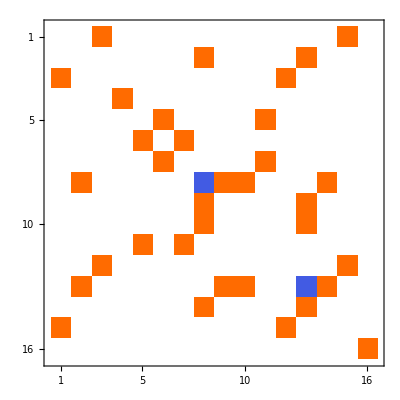

```mathematica
MatrixPlot[N[Hdiag]]
```

# Symmetric states

```mathematica
L=5;
noise=Table[1*RandomReal[{-1,1}],{i,L}];
H=HeisenbergXXXwNoise[noise,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
La=6;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,eigenvec},DistributedContexts->Full];
```

```mathematica
eigenvecentropy =Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of E_i, Open XXZ, L = "<>ToString[L]<>", La = "<>ToString[La]<>", Δ = "<>ToString[Δ]<>"",35,Black],PlotStyle->{Directive[Gray,Opacity[0.5]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

-Graphics-

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
ListPlot[Transpose[{energies,iprs}],PlotRange->All,ImageSize->600]
```

-Graphics-

```mathematica
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
productstate=data[[1;;10]][[All,3]];
(*tlist=Table[10^i,{i,-1,3,0.0008}];
tlist//Length*)
ti=0;
tf=1000;
Δt=0.5;
tlist=Table[i,{i,ti,tf,Δt}];
tlist//Length
```

2001

```mathematica
fakesvn=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

```mathematica
longmean=Table[Mean[fakesvn[[i]][[All,2]][[-500;;-1]]],{i,Length[productstate]}];
newenergies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate}];
```

```mathematica
(*Step 1:Determine the overall energy range*)
sorted=data[[1;;10]][[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
(*Step 2:Define a function to map an energy value to a temperature-like color*)
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListPlot[fakesvn[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", Δ = "<>ToString[Δ]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots,Plot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Black,Dashed]}]}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
```

-Graphics-

```mathematica
Show[{eigenvecentropy,Table[ListPlot[{{newenergies[[i]],longmean[[i]]}},PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}]}]
```

-Graphics-